Wolfram Online Mini Campus. Part 15

Instagram Posts
Pinterest Posts
"Translation" of SageMath Online Mini Campus. Part 15

Color Exploration

```mathematica
CNC=ColorData["Crayola","ColorRules"]; CNC[[1;;5]]
Show[Table[PolarPlot[Sin[5θ]^2+.02*i,{θ,0,2Pi},PlotStyle->Values[CNC][[i]]],
                   { i ,100}],Axes->False]
```

{Almond→RGBColor[0.9372549019607843, 0.8705882352941177, 0.803921568627451],AntiqueBrass→RGBColor[0.803921568627451, 0.5843137254901961, 0.4588235294117647],Apricot→RGBColor[0.9921568627450981, 0.8509803921568627, 0.7098039215686275],Aquamarine→RGBColor[0.47058823529411764, 0.8588235294117647, 0.8862745098039215],Asparagus→RGBColor[0.5294117647058824, 0.6627450980392157, 0.4196078431372549]}

-Graphics-

```mathematica
LNC=ColorData["Legacy","ColorRules"]; LNC[[1;;5]]
Show[Table[PolarPlot[i*(2Cos[4θ]-Exp[Cos[θ]^2-Sin[θ]]),{θ,0,2Pi},
                                          PlotStyle->Values[LNC][[i]]],{ i ,100}],Axes->False]
```

{AliceBlue→RGBColor[0.941206, 0.972503, 1.0],AlizarinCrimson→RGBColor[0.889996, 0.149998, 0.209998],Antique→RGBColor[0.980575, 0.92233, 0.844661],Apricot→RGBColor[1.0, 0.340007, 0.129994],Aquamarine→RGBColor[0.498001, 1.0, 0.831401]}

-Graphics-

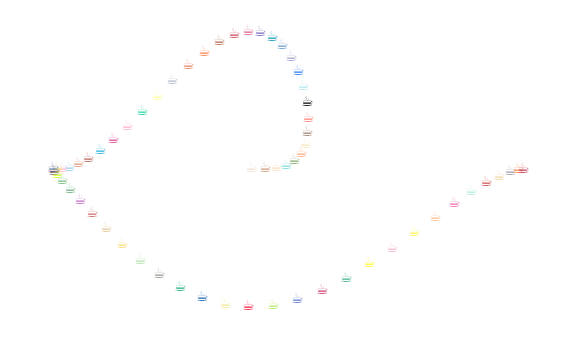

```mathematica
XY=Table[{Cos[t]Log[t+1],Sin[t]^3 },{t,0,2Pi,.1}]; PM={"☕","⚖","☘","⚜","⚙"};
SM[marker_,i_]:=Text[Style[marker,14,Values[ColorData["Crayola","ColorRules"]][[i]],
                                                FontVariations->{"Underline" -> True}],XY[[i]]];
GTP[marker_]:=Graphics[Table[SM[marker,i],{i,63}]];
Show[GTP[PM[[1]]],ImageSize->Large]
```

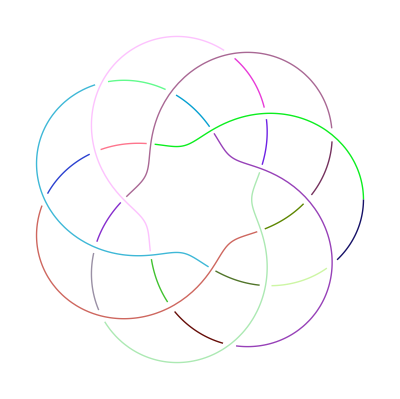
-Graphics3D-→-Graphics-

```mathematica
KDSC=KnotData[{"TorusKnot",{4,7}},"SpaceCurve"];
KDD=KnotData[{"TorusKnot", {4,7}},"KnotDiagramData"];
VLCR=Values[ColorData["Legacy","ColorRules"]];
Graphics3D[{Flatten[Table[{VLCR[[Floor[t/.033+1]]],Text["☸",KDSC[t]]},{t,0,2Pi,.033}]],
                        LightBlue,Opacity[.05],EdgeForm[None],Cuboid[{-3,-3,-1},{3,3,1}]},Boxed->False]->
Graphics[Transpose[{Table[RGBColor@@RandomReal[{0,1},3],{Length[#]}],#}]]&@KDD
```

```mathematica
Multicolumn[Table[ParametricPlot3D[Table[{z x y^2,z y x^2,Exp[.5(x^2+y^3)]},{z,-1,1,.5}],
                                 {x,-1,1},{y,-1,1},PlotRange->All,Mesh->False,Boxed->False,Axes->False,
             ImageSize->Small,ColorFunction->c,PlotLabel->c],
              {c,{"IslandColors","CherryTones","PearlColors","NeonColors",
                   "AvocadoColors","SunsetColors","AuroraColors","Pastel"}}],4]
```

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
GPD[p_,c1_,c2_,r_]:=Graphics3D[{RGBColor[c1],Opacity[.5],Sphere[{0,0,0},r],
                        EdgeForm[{RGBColor[c2],Thickness[.007]}],Transparent,
         PolyhedronData[{p,#}, "GraphicsComplex"]&/@{"Laevo","Dextro"}},Boxed->False];
{GPD["PentagonalHexecontahedron","royalblue","silver",3.45],
GPD["SnubDodecahedron","crimson","gold",1.95]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
PolyhedronData["SnubDodecahedron","Insphere"]
```

Missing[NotApplicable]

```mathematica
PEC=Function[{p},Table[{PolyhedronData[p,"VertexCoordinates"][[PolyhedronData[p,"Edges"][[i,1]]]],
                                                      PolyhedronData[p,"VertexCoordinates"][[PolyhedronData[p,"Edges"][[i,2]]]]},
                                  {i,Length[PolyhedronData[p,"Edges"]]}]];
Table[Graphics3D[{Tube[PEC[p],.05],FaceForm[Opacity[.75],White],
                                   Transpose[{ColorData["Crayola","ColorList"][[11;;10+Length[#]]],#}]},
                      Boxed->False]&@PolyhedronData[p,"Polygons"],
    {p,{"HexakisIcosahedron","DeltoidalHexecontahedron"}}]
```

{-Graphics3D-,-Graphics3D-}

Exploration of Functions

```mathematica
f1=2^x; f2=2x-x^2; x1=0; x2=2; y1=0; y2=4; s=Integrate[f1-f2,{x,x1,x2}];
l=Join[Prepend[Table[{.02i,2^(.02*i)}, {i,100}],{0,0}],
               Table[{.02i,.04i-.0004i^2}, {i,100,0,-1}]];
pp1=Plot[{f1,f2},{x,x1,x2},Filling->True,FillingStyle->RGBColor["#3636ff"],
                      PlotStyle->Directive[RGBColor["silver"],Thickness[.02]],Frame->True,AspectRatio->1,
         Epilog->{Directive[RGBColor["silver"],Thickness[.02]],Line[{{{0,0},{0,1}},{{2,4},{2,0}}}]}];
pp3=RegionPlot[f2<y<f1,{x,x1,x2},{y,y1,y2},Mesh->All,PlotStyle->RGBColor["#3636ff"],
                                   MeshStyle->Directive[RGBColor["silver"],Thickness[.001]]];
pp2=Graphics[{RGBColor["#3636ff"],EdgeForm[{RGBColor["silver"],Thickness[.02]}],
                               Polygon[l]},AspectRatio->1,Frame->True, PlotLabel->s->N[s]];                                    
{pp1,pp2,pp3}
```

{-Graphics-,-Graphics-,-Graphics-}

Exploration of Associations

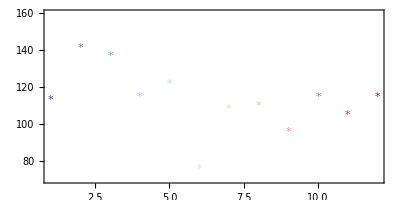

```mathematica
LA={<|"year"->2017,"month"->"Jan","temperature"->113.|>,<|"year"->2017,"month"->"Feb","temperature"->141.|>,
         <|"year"->2017,"month"->"Mar","temperature"->137.|>,<|"year"->2017,"month"->"Apr","temperature"->115.|>,
         <|"year"->2017,"month"->"May","temperature"->122.|>,<|"year"->2017,"month"->"Jun","temperature"->76.|>,
         <|"year"->2017,"month"->"Jul","temperature"->108.|>,<|"year"->2017,"month"->"Aug","temperature"->110.|>,
         <|"year"->2017,"month"->"Sep","temperature"->96.|>,<|"year"->2017,"month"->"Oct","temperature"->115.|>,
         <|"year"->2017,"month"->"Nov","temperature"->105.|>,<|"year"->2017,"month"->"Dec","temperature"->115.|>,
    <|"year"->2018,"month"->"Jan","temperature"->103.|>,<|"year"->2018,"month"->"Feb","temperature"->114.|>,
         <|"year"->2018,"month"->"Mar","temperature"->121.|>,<|"year"->2018,"month"->"Apr","temperature"->120.|>,
         <|"year"->2018,"month"->"May","temperature"->100.|>,<|"year"->2018,"month"->"Jun","temperature"->86.|>,
         <|"year"->2018,"month"->"Jul","temperature"->106.|>,<|"year"->2018,"month"->"Aug","temperature"->90.|>,
         <|"year"->2018,"month"->"Sep","temperature"->89.|>,<|"year"->2018,"month"->"Oct","temperature"->111.|>,
         <|"year"->2018,"month"->"Nov","temperature"->97.|>,<|"year"->2018,"month"->"Dec","temperature"->121.|>}; 
Show[Table[Graphics[{ColorData["ThermometerColors"][.08i],
                                      Style[Text["*",{i,LA[[i]]["temperature"]}],20]}],{i,12}],
         AspectRatio->1/2,Frame->True,PlotRange->{Automatic,{70,160}},
   FrameTicks->{Table[{i,LA[[i]]["month"]},{i,12}],Automatic}]
```

```mathematica
DLA=Dataset[LA]
```

Exploration of D3.js Objects

```mathematica
EmbeddedHTML["<body><script src='//d3js.org/d3.v3.min.js'></script><script>
var mouse=[330,330],count=0;
var svg=d3.select('body').append('svg').attr('width',650).attr('height',650);
var g=svg.selectAll('g').data(d3.range(25)).enter().append('g').attr('transform','translate('+mouse+')');
g.append('rect').attr('rx',7).attr('ry',7).attr('x',-12.5).attr('y',-12.5).attr('width',20).attr('height',20)
               .attr('transform',function(d,i){return 'scale('+(1-d/25)*20+')';}).style('fill',d3.scale.category20b());
g.datum(function(d){return {center:mouse.slice(),angle:0};});
svg.append('text').attr('y',20).text('=> https://bl.ocks.org/mbostock/1123639');
svg.on('mousemove',function(){mouse=d3.mouse(this);});
d3.timer(function(){count++;
g.attr('transform',function(d,i){d.center[0]+=(mouse[0]-d.center[0])/(i+1); d.center[1]+=(mouse[1]-d.center[1])/(i+1); 
                             d.angle+=Math.sin((count+i)/40)*7; return 'translate('+d.center+')rotate('+d.angle+')'});});
</script></body>",ImageSize->{700,700}]
```

Null<body><script src='//d3js.org/d3.v3.…'+d.angle+')'});});
</script></body><body><script src='//d3js.org/d3.v3.min.js'></script><script>
var mouse=[330,330],count=0;
var svg=d3.select('body').append('svg').attr('width',650).attr('height',650);
var g=svg.selectAll('g').data(d3.range(25)).enter().append('g').attr('transform','translate('+mouse+')');
g.append('rect').attr('rx',7).attr('ry',7).attr('x',-12.5).attr('y',-12.5).attr('width',20).attr('height',20)
               .attr('transform',function(d,i){return 'scale('+(1-d/25)*20+')';}).style('fill',d3.scale.category20b());
g.datum(function(d){return {center:mouse.slice(),angle:0};});
svg.append('text').attr('y',20).text('=> https://bl.ocks.org/mbostock/1123639');
svg.on('mousemove',function(){mouse=d3.mouse(this);});
d3.timer(function(){count++;
g.attr('transform',function(d,i){d.center[0]+=(mouse[0]-d.center[0])/(i+1); d.center[1]+=(mouse[1]-d.center[1])/(i+1); 
                             d.angle+=Math.sin((count+i)/40)*7; return 'translate('+d.center+')rotate('+d.angle+')'});});
</script></body>